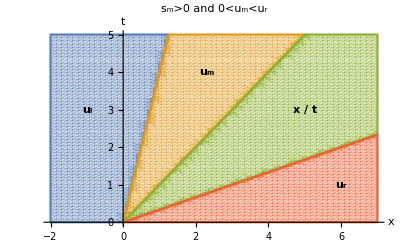

```mathematica
ul = -.5;
um = 1;
ur = 3;
sm = (ul + um)/2;
a=-2;
b =7;
Show[Plot[{x/ur},{x,0,b}],RegionPlot[{t>0&&x<sm*t,t>0&&x>sm*t&&x<um*t,t>0&&x>um*t && x <ur*t,t>0&&x>ur*t},{x,a,b},{t,0,5},PlotPoints->60],Graphics[{Text[Style["u_l",Bold,Large],{-1,3}],Text[Style["u_m",Bold,Large],{2.3,4}],Text[Style["x / t",Bold,Large],{5,3}],Text[Style["u_r",Bold,Large],{6,1}]}],PlotRange->{{a,b},{0,5}},AxesLabel->{Style["x",Medium,Bold],Style["t",Medium,Bold]},PlotLabel->Style["s_m>0 and 0<u_m<u_r",Large]]
```

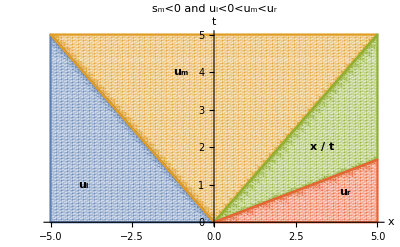

```mathematica
ul = -3;
um = 1;
ur = 3;
sm = (ul + um)/2;
a=-5;
b =5;
Show[Plot[{x/ur},{x,0,b}],RegionPlot[{t>0&&x<sm*t,t>0&&x>sm*t&&x<um*t,t>0&&x>um*t && x <ur*t,t>0&&x>ur*t},{x,a,b},{t,0,5},PlotPoints->60],Graphics[{Text[Style["u_l",Bold,Large],{-4,1}],Text[Style["u_m",Bold,Large],{-1,4}],Text[Style["x / t",Bold,Large],{3.3,2}],Text[Style["u_r",Bold,Large],{4,.8}]}],PlotRange->{{a,b},{0,5}},AxesLabel->{Style["x",Medium,Bold],Style["t",Medium,Bold]},PlotLabel->Style["s_m<0 and u_l<0<u_m<u_r",Large]]
```

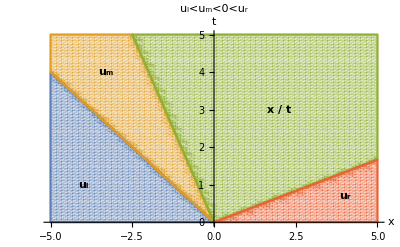

```mathematica
ul = -2;
um = -.5;
ur = 3;
sm = (ul + um)/2;
a=-5;
b =5;
Show[Plot[{x/sm},{x,a,0}],Plot[{x/ur},{x,0,b}],RegionPlot[{t>0&&x<sm*t,t>0&&x>sm*t&&x<um*t,t>0&&x>um*t && x <ur*t,t>0&&x>ur*t},{x,a,b},{t,0,5},PlotPoints->60],Graphics[{Text[Style["u_l",Bold,Large],{-4,1}],Text[Style["u_m",Bold,Large],{-3.3,4}],Text[Style["x / t",Bold,Large],{2,3}],Text[Style["u_r",Bold,Large],{4,.7}]}],PlotRange->{{a,b},{0,5}},AxesLabel->{Style["x",Medium,Bold],Style["t",Medium,Bold]},PlotLabel->Style["u_l<u_m<0<u_r",Large],Axes->True,Frame->False]
```

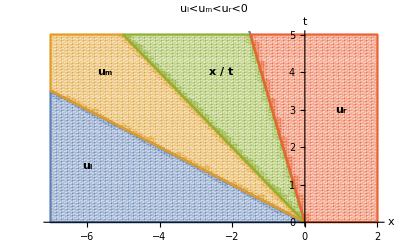

```mathematica
ul = -3;
um = -1;
ur = -.3;
sm = (ul + um)/2;
a=-7;
b =2;
Show[Plot[{x/ur},{x,a,0}],RegionPlot[{t>0&&x<sm*t,t>0&&x>sm*t&&x<um*t,t>0&&x>um*t && x <ur*t,t>0&&x>ur*t},{x,a,b},{t,0,5},PlotPoints->60],Graphics[{Text[Style["u_l",Bold,Large],{-6,1.5}],Text[Style["u_m",Bold,Large],{-5.5,4}],Text[Style["x / t",Bold,Large],{-2.3,4}],Text[Style["u_r",Bold,Large],{1,3}]}],PlotRange->{{a,b},{0,5}},AxesLabel->{Style["x",Medium,Bold],Style["t",Medium,Bold]},PlotLabel->Style["u_l<u_m<u_r<0",Large]]
```

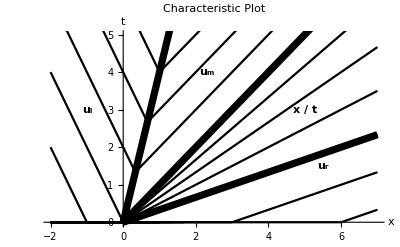

```mathematica
ul = -.5;
um = 1;
ur = 3;
sm = (ul + um)/2;
a=-2;
b =7;
fl[x_,s_] := Piecewise[{{x/ul+s, x/ul+s>=x/sm && x/ul+s ≥0}, {0, True}}]
fm[x_,s_] := Piecewise[{{x/um+s, x/um+s<=x/sm && x/um+s ≥0}, {0, True}}]
fr[x_,s_] := Piecewise[{{x/ur+s, x/ur+s<=x/ur && x/ur+s ≥0}, {0, True}}]
fra[x_,s_] := Piecewise[{{s x/ur, s x/ur>=x/ur && s x/ur≤x/um}, {0, True}}]
Show[Table[Plot[fl[x,s],{x,a,0},PlotStyle->Black],{s,-4,0,2}],
Table[Plot[fl[x,s],{x,a,1},PlotStyle->Black],{s,2,6,2}],
Table[Plot[fm[x,s],{x,a,b},PlotStyle->Black],{s,1,5,1}],
Table[Plot[fr[x,s],{x,a,b},PlotStyle->Black],{s,-2,0,1}],
Table[Plot[fra[x,s],{x,0,b},PlotStyle->Black],{s,1,ur/um,(ur/um - 1)/4}],Plot[{x/um,x/sm,x/ur},{x,0,b},PlotStyle->Directive[Black,Thickness[.013]]],Graphics[{Text[Style["u_l",Bold,Large],{-1,3}],Text[Style["u_m",Bold,Large],{2.3,4}],Text[Style["x / t",Bold,Large],{5,3}],Text[Style["u_r",Bold,Large],{5.5,1.5}]}],PlotRange->{{a,b},{0,5}},AxesLabel->{Style["x",Medium,Bold],Style["t",Medium,Bold]},PlotLabel->Style["Characteristic Plot",Large],Frame->False, Axes->True]
```

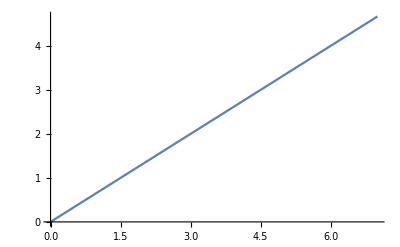

```mathematica
Plot[fra[x,2],{x,0,b}]
```